```mathematica
x1 = 0.5;
x2 = 0.88;
ψ50= -4.5;
ψ88= -6.5;

ci=Log[Log[1.-x1]/Log[1.-x2]]/(Log[-ψ50]-Log[-ψ88])
bi=-ψ50/((-Log[1.-x1])^(1./ci))
```

3.04046

5.0765

```mathematica
1/2Erf[p(ψ95-ψ50s)] + 1/2== q
```

```mathematica
Solve[1/2Erf[p(ψ95-ψ50s)] + 1/2== q, p]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→-InverseErf[-1+2 q]/(ψ50s-ψ95)}}

```mathematica
Solve[kT[-ψ] == q,ψ ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ψ→-b (-Log[q])^(1/c)}}

```mathematica
kT[ψ_]:= (Exp[-(ψ/b)^c])
```

```mathematica
k[ψ_]:= (Exp[-(ψ/bi)^ci])
```

```mathematica
ψ95 = Solve[k[-ψ] == 0.95,ψ ][[1,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-1.9112

```mathematica
Solve[1/2Erf[p(ψ95-ψ50)] + 1/2== 0.95, p]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→0.449277}}

```mathematica
ψ05 = Solve[k[-ψ] == 0.05,ψ ][[1,1,2]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

-7.28258

```mathematica
Solve[1/2Erf[p(ψ05-ψ50)] + 1/2== 0.05, p]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{p→0.417989}}

```mathematica
kd[ψ_, p_]:=1/2Erf[p(ψ-ψ50)] + 1/2
```

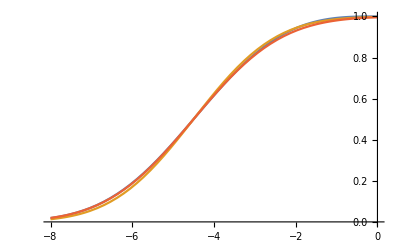

```mathematica
9.2
```

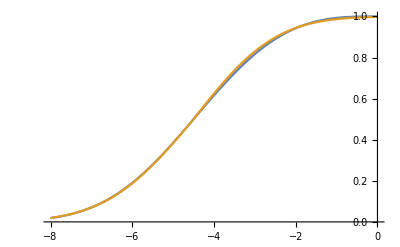

```mathematica
f[ψ_]:=Piecewise[{{kd[ψ, 0.417989],ψ<ψ50},{kd[ψ, 0.4492771686926618],ψ>ψ50}}]
Plot[{k[-ψ],f[ψ]}, {ψ,-8, 0}]
```

```mathematica
9.2/9.3
```

0.989247

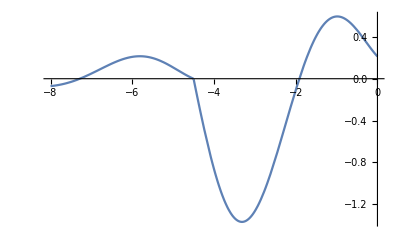

```mathematica
Plot[{k[-ψ]-f[ψ]}*100, {ψ,-8, 0}]
```

```mathematica
ψS = -0.5;
ψL= -4;
org = NIntegrate[k[-ψ], {ψ, ψL,ψS}];
fit= NIntegrate[f[ψ], {ψ, ψL,ψS}];
fitBad =k[(-ψS -ψL)/2] *(ψS-ψL);
(fit-org)*100
(fitBad-org)*100
```

1.35517

13.7301

```mathematica
ψS = -0.5;
ψL= -2.5;
org = NIntegrate[k[-ψ], {ψ, ψL,ψS}]
fit= NIntegrate[f[ψ], {ψ, ψL,ψS}]
fitBad =k[(-ψS -ψL)/2] *(ψS-ψL)
(fit-org)*100
(fitBad-org)*100
```

1.93061

1.92654

1.95149

-0.406922

2.08743

```mathematica
Clear[ψ50]

FullSimplify@Integrate[1/2Erf[s(ψ-ψ50)] + 1/2,ψ]
```

1/2 ((ⅇ^(-s^2 (ψ-ψ50)^2))/(√π s)+ψ+(ψ-ψ50) Erf[s (ψ-ψ50)])

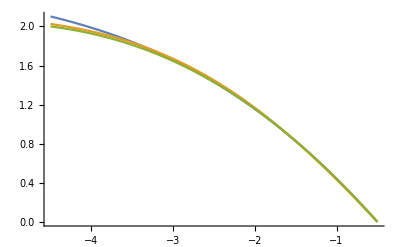

2.10183

2.02481

2.

```mathematica
ψS = -0.5;
Plot[{NIntegrate[k[-ψ], {ψ, ψL,ψS}],
NIntegrate[f[ψ], {ψ, ψL,ψS}],k[(-ψS -ψL)/2] *(ψS-ψL)}, {ψL, -0.5, -4.5}]
ψL = -4.5;
org = NIntegrate[k[-ψ], {ψ, ψL,ψS}]
fit= NIntegrate[f[ψ], {ψ, ψL,ψS}]
fitBad =k[(-ψS -ψL)/2] *(ψS-ψL)
```

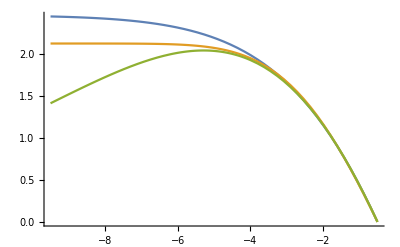

2.44528

2.12322

1.41199

0.1

```mathematica
ψS = -0.5;
Plot[{NIntegrate[k[-ψ], {ψ, ψL,ψS}],
NIntegrate[f[ψ], {ψ, ψL,ψS}],
k[(-ψS -ψL)/2] *(ψS-ψL)}, {ψL, -0.5, -9.5}]
ψL = -9.5;
org = NIntegrate[k[-ψ], {ψ, ψL,ψS}]
fit= NIntegrate[f[ψ], {ψ, ψL,ψS}]
fitBad =k[(-ψS -ψL)/2] *(ψS-ψL)
```

```mathematica
k[(-ψS -ψL)/2]
```

0.714679

```mathematica
Clear@h
```

```mathematica
ρ= 1000;
g = 10
```

10

```mathematica
ρ*g*h /10^6
```

1

```mathematica
Integrate[ρ*g/10^6, {h, 0, H}]
```

1

```mathematica
ψs[h_]:= Rescale[h,{0,H}, {-ψS,-ψL}]
```

0.715519

1.35949

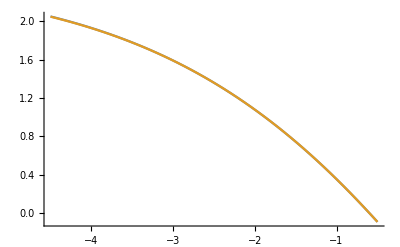

```mathematica
ψXXX[h_]:= Rescale[h,{0,H}, {-ψS,-ψL}]
ψL = -2.5;
ψS = -0.5;
Plot[{
NIntegrate[k[-ψ] , {ψ, ψL,ψS}]-k[(-ψS -ψL)/2]*ψH,
NIntegrate[k[-ψ] , {ψ, ψL,ψS}]-Integrate[k[ψXXX[h]]ρ*g/10^6, {h, 0, H}]}, {ψL, -0.5, -4.5}]
ψL = -2.5;
```

```mathematica
NIntegrate[k[ψXXX[h]]ρ*g/10^6, {h, 0, H}]
```

0.0604746

```mathematica
ρ*g/10^6*NIntegrate[k[ψXXX[h]] ,{h, 0, H}]
```

0.0604746

```mathematica
ρ*g/10^6* H*NIntegrate[k[-ψ] ,{ψ, ψL,ψS}]
```

0.0604746

```mathematica
NIntegrate[k[-ψ], {ψ, ψL ,ψS }]
```

```mathematica
ψL = -2.5;
ψS = -1.6;
H =10;
ψH = ρ g H/10^6;
org = NIntegrate[k[-ψ], {ψ, ψL ,ψS }]-NIntegrate[k[ψXXX[h]]ρ*g/10^6, {h, 0, H}]

simp =k[(-ψS -ψL)/2] *(ψS-ψL -ψH)

(1-ρ*g/10^6* H/(ψS-ψL)) NIntegrate[k[-ψ], {ψ, ψL ,ψS }]
```

0.475032

0.474129

0.475032

```mathematica
ψXXX[h_]:= Rescale[h,{0,H}, {-ψS,-ψL}]
Integrate[ψXXX[h] ,{h, 0, H}]
```

15.

```mathematica
NIntegrate[k[ψXXX[h]]ρ*g/10^6, {h, 0, H}]
```

0.0715519

```mathematica
NIntegrate[k[ψ]ρ*g/10^6* H/(ψL-ψS) , {ψ,-ψS,-ψL}]
```

-0.0715519

```mathematica
ψXXX[h]
```

-ψSs+(h (-ψLs+ψSs))/Hs

```mathematica
D[ψXXX[h],h]
```

(-ψLs+ψSs)/Hs

```mathematica
ScientificForm[0.3023730310953042]
```

3.02373×10^-1

```mathematica
Rescale[h,{0,Hh}, {-ψSh,-ψLh}]
```

-ψSh+(h (-ψLh+ψSh))/Hh

```mathematica
Rescale[ψ,{ψSh,ψLh},{0,Hh}]
```

(Hh ψ)/(ψLh-ψSh)-(Hh ψSh)/(ψLh-ψSh)

```mathematica
NIntegrate[k[-ψ], {ψ, ψL ,ψS }]
```

0.604746

```mathematica
ρ g H
```

100000

```mathematica
NIntegrate[k[ψXXX[h]], {h, 0, H}]
```

54.4271

```mathematica
ψXXX[h_]:= Rescale[h,{0,H}, {ψS,ψL}]
ψL = 4.5;
ψS = 1.5;
H =90;
ψH = ρ g H/10^6;
org = NIntegrate[k[ψ], {ψ, ψS ,ψL }]-NIntegrate[k[ψXXX[h]]ρ*g/10^6, {h, 0, H}]

simp =k[(ψL+ψS)/2] *(ψL -ψS-ψH)
```

0.892875

0.855806

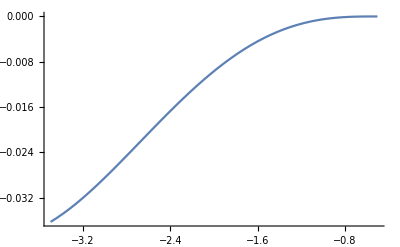

```mathematica
Plot[{NIntegrate[k[-ψ], {ψ, ψL,ψS}]-k[(-ψS -ψL)/2] *(ψS-ψL)}, {ψL, -0.5,ψ50}]
```

```mathematica
val = Table[{ψL, NIntegrate[k[-ψ], {ψ, ψL,ψS}]-k[(-ψS -ψL)/2] *(ψS-ψL)}, {ψL, ψ50, -0.5, 0.01}];
```

```mathematica
Manipulate[Show[Plot[(Exp[- α Abs[x]^4])-1, {x,ψ50,0}], ListPlot[val]], {α, 0, 0.1}]
```

ListPlot::lpn: val is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[val]].

```mathematica
nlm=NonlinearModelFit[val,(Exp[- α Abs[x]^4])-1,{{α,0.0006}},x]
nlm["ParameterTable"]
```

FittedModel[-1+ⅇ^(-0.000570006 (Abs«1»«1»])^4)]

General::munfl: Exp[-1545.14] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
α | 0.000570006 | 6.03713×10^-7 | 944.167 | 0.

```mathematica
f[x_]:= Min[Exp[-x],Sin[x]]
```

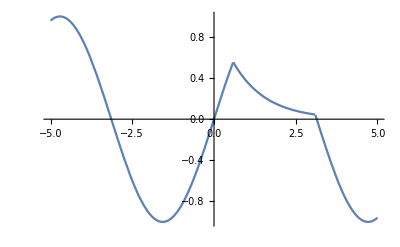

```mathematica
Plot[f[x],{x,-5,5}]
```

```mathematica
NIntegrate[f[x],{x,-1,1}]
```

-0.104192